```mathematica
triples=Rest[Import["/Users/lithium/Downloads/BPS-spectra/coprime_triples.csv"]];
```

```mathematica
triples[[1]]
```

{2,3,5}

```mathematica
var=triples[[1]];
fileName="/Users/lithium/Downloads/BPS-spectra/data/seifert/"<>StringJoin[Riffle[ToString/@var,"_"]]<>".mx";
data=Import[fileName]
```

```mathematica
psiproj[triple_]:=Module[{m,proj,bi,tri,result},
m=Times@@triple;bi=Subsets[triple,{2}];tri=Append[Table[Times@@bi[[i]],{i,1,3}],1];proj=Table[Boole[IntegerQ[(a+b)/(2tri[[n]])]]Boole[IntegerQ[(tri[[n]](a-b))/(2m)]]-Boole[IntegerQ[(-a+b)/(2tri[[n]])]]Boole[IntegerQ[(tri[[n]](a+b))/(2m)]],{n,1,Length[tri]},{a,1,m-1},{b,1,m-1}];
result=Simplify[Plus@@proj];
result
]
```

```mathematica
psicoef[proj_]:=Module[{mvalue,matrix,positions,values,n,m,i,j},
mvalue=Length[proj]+1;
matrix=DeleteDuplicates[RowReduce[proj]]//Select[#=!=ConstantArray[0,Length[#]]&];{n,m}=Dimensions[matrix];
positions=Table[Position[matrix[[i]],_?(#!=0&)]//Flatten,{i,1,Length[matrix]}];
values=Table[Extract[matrix[[i]],positions[[i,j]]],{i,1,n},{j,1,Length[positions[[i]]]}];{positions,values,mvalue}]
```

```mathematica
Do[
var=triples[[i]];
fileName="/Users/lithium/Downloads/BPS-spectra/data/seifert/projections/"<>StringJoin[Riffle[ToString/@var,"_"]]<>".mx";
proj=psiproj[var];
co=psicoef[proj];
Export[fileName,co],{i,101,150}
]
```

```mathematica
psi[m_,r_,trunc_]:=Module[{series=0,expo=0,n},
n=1;While[expo<=trunc,n++;expo=r^2/(4m)+n r+m n^2;series+= q^expo];n=0;While[expo<=trunc,n--;expo=r^2/(4m)+n r+m n^2;series+=(-1)^n q^expo;];series]
```

```mathematica
psiindex[coef_,trunc_]:=Module[{pos,val,len,m,poly,lowest,cof,expo},
m=coef[[3]];pos=coef[[1]];val=coef[[2]];len=Length[pos];
poly=Table[Sum[psi[m,pos[[n,i]],trunc],{i,1,4}],{n,1,len}];
expo=Table[Exponent[poly[[n]],q,List],{n,1,len}];
cof=Table[Table[Coefficient[poly[[n]],q^(expo[[n,i]])],{i,1,Length[expo[[n]]]}],{n,1,len}];
lowest=Table[expo[[n,1]],{n,1,len}];
expo=Table[Exponent[poly[[n]]/q^lowest[[n]],q,List],{n,1,len}];
{expo,cof,lowest}
]
```

```mathematica
psi2[m_,r_,trunc_]:=Module[{series=0,expo=0,newtrunc,n},
n=1;newtrunc=Ceiling[trunc/2]+10;For[n=1,n<=newtrunc,n++,expo=r^2/(4m)+n r+m n^2;series+= q^expo];n=0;For[n=0,n>=-newtrunc,n--,expo=r^2/(4m)+n r+m n^2;series+=(-1)^n q^expo;];series]
```

```mathematica
index2[coef_,trunc_]:=Module[{pos,val,len,m,poly,lowest,cof,expo},
m=coef[[3]];pos=coef[[1]];val=coef[[2]];len=Length[pos];
poly=Table[Sum[val[[n,i]]psi2[m,pos[[n,i]],trunc],{i,1,4}],{n,1,len}];
expo=Table[Take[Exponent[poly[[n]],q,List],trunc],{n,1,len}];
cof=Table[Table[Coefficient[poly[[n]],q^(expo[[n,i]])],{i,1,Length[expo[[n]]]}],{n,1,len}];
lowest=Table[expo[[n,1]],{n,1,len}];
expo=Table[expo[[n,i]]-lowest[[n]],{n,1,len},{i,1,trunc}];
{expo,cof,lowest}
]
```

```mathematica
Do[
var=triples[[i]];
fileName="/Users/lithium/Downloads/BPS-spectra/data/seifert/";
data=Import[fileName<>"projections/"<>StringJoin[Riffle[ToString/@var,"_"]]<>".mx"];
index=index2[data,100];
Export[fileName<>"series/"<>StringJoin[Riffle[ToString/@var,"_"]]<>"_expo.csv",index[[1]]];
Export[fileName<>"series/"<>StringJoin[Riffle[ToString/@var,"_"]]<>"_coef.csv",index[[2]]];
Export[fileName<>"series/"<>StringJoin[Riffle[ToString/@var,"_"]]<>"_pref.csv",index[[3]]],{i,1,150}]
```

Import::nffil: File /Users/lithium/Downloads/BPS-spectra/data/seifert/projections/2_7_19.mx not found during Import.

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
,
```

```mathematica
var=triples[[1]];
data=Import["/Users/lithium/Downloads/BPS-spectra/data/seifert/projections/2_3_11.mx"];
ind=psiindex[data,100];
ind2=index2[data,100];
```

```mathematica
Times@@var
data[[1]]
```

30

{{1,23,43,65},{5,17,49,61},{7,29,37,59},{13,31,35,53},{19,25,41,47}}

```mathematica
psi[30,23,1000]
```

q^(20449/120)+q^(41209/120)+q^(69169/120)+q^(104329/120)+q^(146689/120)

```mathematica
ind[[1]]
ind2[[1]]
```

{{0,46,91,144},{0,25,97,126},{0,47,65,117},{0,39,48,90},{0,13,49,63}}

{{0,2,7,16,17,30,45,65,67,91,116,147,150,185,220,262,266,312,357,410,415,472,527,591,597,665,730,805,812,891,966,1052,1060,1150,1235,1332,1341,1442,1537,1645,1655,1767,1872,1991,2002,2125,2240,2370,2382,2516,2641,2782,2795,2940,3075,3227,3241,3397,3542,3705,3720,3887,4042,4216,4232,4410,4575,4760,4777,4966,5141,5337,5355,5555,5740,5947,5966,6177,6372,6590,6610,6832,7037,7266,7287,7520,7735,7975,7997,8241,8466,8717,8740,8995,9230,9492,9516,9782,10027,10300},{0,1,9,14,19,26,50,61,71,84,124,141,156,175,231,254,274,299,371,400,425,456,544,579,609,646,750,791,826,869,989,1036,1076,1125,1261,1314,1359,1414,1566,1625,1675,1736,1904,1969,2024,2091,2275,2346,2406,2479,2679,2756,2821,2900,3116,3199,3269,3354,3586,3675,3750,3841,4089,4184,4264,4361,4625,4726,4811,4914,5194,5301,5391,5500,5796,5909,6004,6119,6431,6550,6650,6771,7099,7224,7329,7456,7800,7931,8041,8174,8534,8671,8786,8925,9301,9444,9564,9709,10101,10250},{0,3,5,13,20,34,40,59,73,98,108,138,159,195,209,250,278,325,343,395,430,488,510,573,615,684,710,784,833,913,943,1028,1084,1175,1209,1305,1368,1470,1508,1615,1685,1798,1840,1958,2035,2159,2205,2334,2418,2553,2603,2743,2834,2980,3034,3185,3283,3440,3498,3660,3765,3933,3995,4168,4280,4459,4525,4709,4828,5018,5088,5283,5409,5610,5684,5890,6023,6235,6313,6530,6670,6893,6975,7203,7350,7584,7670,7909,8063,8308,8398,8648,8809,9065,9159,9420,9588,9855,9953,10225},{0,3,4,10,23,35,38,53,79,100,105,129,168,198,205,238,290,329,338,380,445,493,504,555,633,690,703,763,854,920,935,1004,1108,1183,1200,1278,1395,1479,1498,1585,1715,1808,1829,1925,2068,2170,2193,2298,2454,2565,2590,2704,2873,2993,3020,3143,3325,3454,3483,3615,3810,3948,3979,4120,4328,4475,4508,4658,4879,5035,5070,5229,5463,5628,5665,5833,6080,6254,6293,6470,6730,6913,6954,7140,7413,7605,7648,7843,8129,8330,8375,8579,8878,9088,9135,9348,9660,9879,9928,10150},{0,1,5,7,26,30,42,47,85,92,112,120,177,187,215,226,302,315,351,365,460,476,520,537,651,670,722,742,875,897,957,980,1132,1157,1225,1251,1422,1450,1526,1555,1745,1776,1860,1892,2101,2135,2227,2262,2490,2527,2627,2665,2912,2952,3060,3101,3367,3410,3526,3570,3855,3901,4025,4072,4376,4425,4557,4607,4930,4982,5122,5175,5517,5572,5720,5776,6137,6195,6351,6410,6790,6851,7015,7077,7476,7540,7712,7777,8195,8262,8442,8510,8947,9017,9205,9276,9732,9805,10001,10075}}

```mathematica
Do[
var=triples[[i]];
fileName="/Users/lithium/Downloads/BPS-spectra/data/seifert/";
data=Import[fileName<>"projections/"<>StringJoin[Riffle[ToString/@var,"_"]]<>".mx"];
index=psiindex[data,50000];
Export[fileName<>"series/"<>StringJoin[Riffle[ToString/@var,"_"]]<>"_expo.csv",index[[1]]];
Export[fileName<>"series/"<>StringJoin[Riffle[ToString/@var,"_"]]<>"_coef.csv",index[[2]]];
Export[fileName<>"series/"<>StringJoin[Riffle[ToString/@var,"_"]]<>"_pref.csv",index[[3]]],{i,1,150}]
```

Import::nffil: File /Users/lithium/Downloads/BPS-spectra/data/seifert/projections/2_7_19.mx not found during Import.

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
Length[data[[1]]]
```

2

```mathematica
Floor[3/2]//N
```

Integer[1.5]

```mathematica
s=psi[66,29,10000]
```

q^(85849/264)-q^(180625/264)+q^(310249/264)-q^(474721/264)+q^(674041/264)-q^(908209/264)+q^(1177225/264)-q^(1481089/264)+q^(1819801/264)-q^(2193361/264)+q^(2601769/264)-q^(3045025/264)

```mathematica
expo=Exponent[s,q,List]
%//Length
```

{85849/264,180625/264,310249/264,474721/264,674041/264,908209/264,1177225/264,1481089/264,1819801/264,2193361/264,2601769/264,3045025/264}

12

```mathematica
Table[Coefficient[s,q^(expo[[n]])],{n,1,Length[expo]}]
%//Length
```

{1,-1,1,-1,1,-1,1,-1,1,-1,1,-1}

12

```mathematica
s
Exponent[s,q]
```

q^(85849/264)-q^(180625/264)+q^(310249/264)-q^(474721/264)+q^(674041/264)-q^(908209/264)+q^(1177225/264)-q^(1481089/264)+q^(1819801/264)-q^(2193361/264)+q^(2601769/264)-q^(3045025/264)

1[85849/264,180625/264,310249/264,474721/264,674041/264,908209/264,1177225/264,1481089/264,1819801/264,2193361/264,2601769/264,3045025/264]

```mathematica
Coefficient[s,q]
```

0

```mathematica
alpha=x/y
y/(x+y)=1/(alpha+1)
```

```mathematica
EulerPhi[606]/4
```

50

```mathematica
Sum[EulerPhi[Times@@triples[[i]]]/4,{i,1,150}]
```

10022

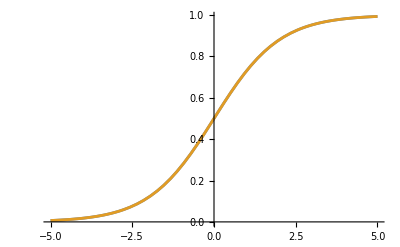

```mathematica
Plot[{LogisticSigmoid[x],1/(1+E^(-x))},{x,-5,5}]
```

```mathematica
LogisticSigmoid
```

LogisticSigmoid